```mathematica
(************************Program Mahdi Molavi************************)
(********* git hub : https://github.com/mahdipc/mathematica*************)
```

```mathematica
Remove["Global`*"];
Clear["Global`*"];
ν[Ι_]:=Module[{i=Ι},
sol=Sort[v/.Solve[ChebyshevU[n+1,v]==0,v],Less];
Return[sol[[i]]];
];
χ[Ι_]:=Module[{i=Ι},
sol=Sort[v/.Solve[ChebyshevT[k+1,v]==0,v],Less];
Return[sol[[i]]];
];
τ[Ι_]:=Module[{i=Ι+1},
If[i== 1,Return[0];];
If[i==k+1,Return[1];];
Return[1/2((2 χ[i]-(χ[k+1]+χ[1]))/(χ[k+1]-χ[1])+1)];
];
𝓉[Ι_]:=Module[{i=Ι+1},
If[i==1,Return[0]];
If[i== n+1,Return[1]];
Return[1/2((2 ν[i]-(ν[n+1]+ν[1]))/(ν[n+1]-ν[1])+1)];
];
𝓉[J_,Ι_]:=Module[{i=Ι,j=J},
h=𝓉[i]-𝓉[i-1];
Return[𝓉[i-1]+τ[j] h];
];
ϕ[J_,T_]:=Module[{j=J,t=T},
Return[Product[If[l≠ j,t-τ[l],1],{l,0,k}]/Product[If[l≠ j,τ[j]-τ[l],1],{l,0,k}]];
];
R[Ι_,J_,T_]:=Module[{i=Ι,j=J,t=T},
Return[Product[If[l≠ j,(t-𝓉[l,i]),1],{l,0,k}]/(t-𝓉[j,i])];
];
ϕ[J_,Ι_,T_]:=Module[{i=Ι,j=J,t=T},
(*
If[j==0 && i==1,
Return[Piecewise[{{R[1,0,t]/R[1,0,𝓉[1,0]],𝓉[0]≤ t≤ 𝓉[1]}},0]];
];
If[1≤ j≤ k-1 && 1≤ i≤ n,Return[Piecewise[{{R[i,j,t]/R[i,j,𝓉[i,j]],𝓉[i-1]≤ t≤ 𝓉[i]}},0]];
];
If[j==k && 1≤ i≤ n-1,
Return[Piecewise[{{∏_(l=0)^(k-1) (t-𝓉[l,i])/(𝓉[k,i]-𝓉[l,i]),𝓉[i-1]≤ t≤ 𝓉[i]},
{∏_(l=1)^k (t-𝓉[l,i+1])/(𝓉[0,i+1]-𝓉[l,i+1]),𝓉[i]≤ t≤ 𝓉[i+1]}},0]];
];
If[j==k && i==n,
Return[Piecewise[{{R[n,k,t]/R[n,k,𝓉[k,n]],𝓉[n-1]≤ t≤ 𝓉[n]}},0]];
];
*)
If[j==0 && i==1,
Return[Piecewise[{{ϕ[0,(t-𝓉[0])/(𝓉[1]-𝓉[0])],𝓉[0]≤ t≤ 𝓉[1]}},0]];
];
If[1≤ j≤ k-1 && 1≤ i≤ n,
Return[Piecewise[{{ϕ[j,(t-𝓉[i-1])/(𝓉[i]-𝓉[i-1])],𝓉[i-1]≤ t≤ 𝓉[i]}},0]];
];
If[j==k && i==n,
Return[Piecewise[{{ϕ[k,(t-𝓉[n-1])/(𝓉[n]-𝓉[n-1])],𝓉[n-1]≤ t≤ 𝓉[n]}},0]];
];
If[j==k && 1≤ i≤ n-1,
Return[Piecewise[{
{ϕ[k,(t-𝓉[i-1])/(𝓉[i]-𝓉[i-1])],𝓉[i-1]≤ t≤ 𝓉[i]},
{ϕ[0,(t-𝓉[i])/(𝓉[i+1]-𝓉[i])],𝓉[i]≤ t≤ 𝓉[i+1]}},
0]];
];
];
ψ[J_,Ι_,T_]:=Module[{i=Ι,j=J,t=T},
If[j==0&& i==1,
Return[Piecewise[{{1,0≤ t≤ 𝓉[1,1]/2}},0]];
];
If[1≤ j≤ k-1 && 1≤ i≤ n,Return[Piecewise[{{1,(𝓉[j-1,i]+𝓉[j,i])/2≤ t≤ (𝓉[j,i]+𝓉[j+1,i])/2}},0]];
];
If[j==k && 1≤ i≤ n-1,Return[Piecewise[{{1,(𝓉[k-1,i]+𝓉[k,i])/2≤ t≤ (𝓉[0,i+1]+𝓉[1,i+1])/2}},0]];
];
If[j==k && i==n,
Return[Piecewise[{{1,(𝓉[k-1,i]+𝓉[k,i])/2≤ t≤ 1}},0]];
];
];
ψ[J_,T_]:=Module[{j=J,t=T},
If[j==0,Return[Piecewise[{{1,0≤ t≤ (τ[0]+τ[1])/2}},0]]];
If[j==k,Return[Piecewise[{{1,(τ[k]+τ[k-1])/2≤ t≤ 1}},0]]];
Return[Piecewise[{{1,(τ[j]+τ[j-1])/2≤ t≤(τ[j]+τ[j+1])/2}},0]];
];
b[Ι_,J_,T_]:=Module[{i=Ι,j=J,t=T},
Return[∫_0^1 ϕ[i,t]ψ[j,t]ⅆt];
];
(*****************************)
AK[s_,t_]=(ⅇ^t Sin[t])/(1+s^2);
AF[t_]=t^3+1/2 ⅇ^t(-1+Log[2])Sin[t];
Ax[t_]=t^3;
k=3;
n=2;
(*****************************)

Ν=n k+1;
ψ[0,2,tt]
(*d[tt_]=Simplify[Flatten[Table[N[ψ[j,i,tt]],{j,0,k},{i,1,n}]]];
b[t_]=Simplify[Flatten[Table[N[ϕ[j,i,t]],{j,0,k},{i,1,n}]]];
VC=Table[Subscript[c, i],{i,1,Ν}];
B=Table[∫_0^1 b[t]⟦i⟧d[t]⟦j⟧ⅆt,{i,1,Ν},{j,1,Ν}];
K=Table[∫_0^1 ∫_0^1 AK[t,s]b[t]⟦i⟧d[t]⟦j⟧ⅆs ⅆt ,{i,1,Ν},{j,1,Ν}];
F=Table[∫_0^1 AF[t]d[t]⟦i⟧ⅆt,{i,1,Ν}];*)
```

j= 0  i=2  n=2  k=3

```mathematica
ANS=(B-K).VC-F;
VC=Flatten[VC/.Solve[ANS==0,VC]]
```

{-1.7791,-1.87941,-1.82572,-1.73316,1.67588/Null,-1.19969,-1.3502}

```mathematica
x[t_]=Simplify[∑_(i=1)^Ν VC⟦i⟧b[t]⟦i⟧]
```

Piecewise[{{1.67588, t>1.||t<0}, {-0.103223-1.24337 t+4.2865 t^2-3.23195 t^3, 0≤t<0.5}, {6.94518-15.3705 t-2.67084 t^2+10.8041 t^3, t==0.5}, {-28.2158+123.234 t-174.326 t^2+80.9836 t^3, True}}]

0.67588

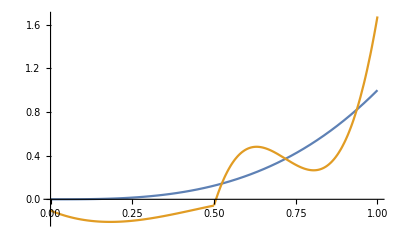

```mathematica
Norm[Flatten[Table[Ax[𝓉[j,i]]-x[𝓉[j,i]],{i,1,n},{j,0,k}]],Infinity]
Plot[{Ax[t],x[t]},{t,0,1}]
```